### Colors

```mathematica
AdinkraGreen = RGBColor[0.10196079,0.61176473,0.21960784];
AdinkraViolet = RGBColor[0.42352942,0.15294118,0.4509804];
AdinkraOrange = RGBColor[0.89803922,0.57647061,0.27450982];
AdinkraRed = RGBColor[0.78431374,0,0.12156863];
```

```mathematica
Clist :={AdinkraGreen,AdinkraViolet,AdinkraOrange,AdinkraRed}
```

```mathematica
ColorData[1,"ColorRules"]
```

{1→RGBColor[0.24720000000000014, 0.24, 0.6],2→RGBColor[0.6, 0.24, 0.4428931686004542],3→RGBColor[0.6, 0.5470136627990908, 0.24],4→RGBColor[0.24, 0.6, 0.33692049419863584],5→RGBColor[0.24, 0.3531726744018182, 0.6],6→RGBColor[0.6, 0.24, 0.5632658430022722],7→RGBColor[0.6, 0.42664098839727194, 0.24],8→RGBColor[0.2634521802031821, 0.6, 0.24],9→RGBColor[0.24, 0.47354534880363613, 0.6],10→RGBColor[0.5163614825959097, 0.24, 0.6],11→RGBColor[0.6, 0.3062683139954558, 0.24],12→RGBColor[0.3838248546049982, 0.6, 0.24],13→RGBColor[0.24, 0.5939180232054561, 0.6],14→RGBColor[0.39598880819409377, 0.24, 0.6],15→RGBColor[0.6, 0.24, 0.2941043604063603]}

```mathematica
Clist:={AdinkraGreen,AdinkraViolet,AdinkraOrange,AdinkraRed,Blue,Yellow,Brown,Purple,Green,Orange,Red,Cyan,Pink,Magenta,Darker[Green],Darker[Yellow]}
```

```mathematica
Clist:={Black}
```

### Other Colors

```mathematica
Color1 = AdinkraGreen;
Color2 = AdinkraViolet;
Color3 = AdinkraOrange;
Color4 = AdinkraRed;
```

```mathematica
Color1 = Red;
Color2 = Darker[Green,0.3];
Color3 = Blue;
Color4 = Black;
```

### Code

```mathematica
blabel=Range[50];
flabel=Range[50];
```

```mathematica
padLmatrix[L_,num_]:=Transpose@ArrayPad[L,{{num,0},{0,num}}]
```

```mathematica
adjacencyToEdge[mat_,col_]:=Return@Select[Flatten[Table[If[mat[[i,j]]=!=0,{i->j,mat[[i,j]]*col},{}],{i,1,Length[mat]},{j,1,Length[mat[[1]]]}],1],#=!={}&]
```

```mathematica
listToEdge[matlist_,num_]:=Return@Sort@Join@Flatten[adjacencyToEdge[padLmatrix[matlist[[#]],num],#]&/@Range[Length[matlist]],1]
```

```mathematica
buildrules[list_]:=Module[{rules={},layerlengths := Map[Length,list,{1}]},
For[i = 1,i≤Length[list],i++,
For[j= 1,j≤layerlengths[[i]],j++,
AppendTo[rules,list[[i]][[j]]->{Range[1-Mean[Range[layerlengths[[i]]]],layerlengths[[i]]+1-layerlengths[[i]]/2][[j]],-(i-1)*1.25}]
]
];
Return@rules
]
```

```mathematica
graphadinkra[matlist_,raise_,num_]:=
GraphPlot[
listToEdge[matlist,num],
EdgeRenderingFunction->(Switch[Sign@#3,
1,{Clist[[Abs@#3]],Thickness[0.005],Line[#1]},
-1,{Clist[[Abs@#3]],Dashing[{0.025,0.047}],Thickness[0.005],Line[#1]}
]&)
,VertexRenderingFunction->(If[#2≤num,
Inset[Graphics[{Black,EdgeForm[Thickness[0.1]],Disk[{0,0},.04],White,Text[Style[flabel[[#2]],Bold,17],{0,0}]},ImageSize->28],#],
Inset[Graphics[{White,EdgeForm[Thickness[0.1]],Disk[{0,0},.04],Black,Text[Style[blabel[[#2]],Bold,17],{0,0}]},ImageSize->28],#]
]&)
,VertexCoordinateRules->raise
]
```

```mathematica
exportadinkra[matlist_,raise_,filename_]:=Export[filename,graphadinkra[matlist,raise]]
```

### Sandbox

```mathematica
L1:={{1,0,0,0},{0,0,0,-1},{0,1,0,0},{0,0,-1,0}}
L2:={{0,1,0,0},{0,0,1,0},{-1,0,0,0},{0,0,0,-1}}
L3:={{0,0,1,0},{0,-1,0,0},{0,0,0,-1},{1,0,0,0}}
L4:={{0,0,0,1},{1,0,0,0},{0,0,1,0},{0,1,0,0}}
```

```mathematica
testlist:={{{1,0,0,0},{0,0,0,-1},{0,1,0,0},{0,0,-1,0}},
{{0,1,0,0},{0,0,1,0},{-1,0,0,0},{0,0,0,-1}},
{{0,0,1,0},{0,-1,0,0},{0,0,0,-1},{1,0,0,0}},
{{0,0,0,1},{1,0,0,0},{0,0,1,0},{0,1,0,0}}}
```

```mathematica
adjacencyToEdge[padLmatrix[r],1]
```

{}

```mathematica
Llist:={{{1,0,0,0},{0,0,0,-1},{0,1,0,0},{0,0,-1,0}},{{0,1,0,0},{0,0,1,0},{-1,0,0,0},{0,0,0,-1}},
{{0,0,1,0},{0,-1,0,0},{0,0,0,-1},{1,0,0,0}},
{{0,0,0,1},{1,0,0,0},{0,0,1,0},{0,1,0,0}}}
```

```mathematica
For[i=1,i≤Length[Llist],i++,Print@adjacencyToEdge[padLmatrix[Llist[[i]]],i]
]
```

{{1→1,{1,0,0,0}},{1→2,{0,0,0,-1}},{1→3,{0,1,0,0}},{1→4,{0,0,-1,0}}}

{{1→1,{0,2,0,0}},{1→2,{0,0,2,0}},{1→3,{-2,0,0,0}},{1→4,{0,0,0,-2}}}

{{1→1,{0,0,3,0}},{1→2,{0,-3,0,0}},{1→3,{0,0,0,-3}},{1→4,{3,0,0,0}}}

{{1→1,{0,0,0,4}},{1→2,{4,0,0,0}},{1→3,{0,0,4,0}},{1→4,{0,4,0,0}}}

```mathematica
Erules:={};
Do[AppendTo[Erules,adjacencyToEdge[padLmatrix[Llist[[i]]],i]],{i,Length@Llist}];
Sort@Join[Erules]
```

{{{1→1,{0,0,0,4}},{1→2,{4,0,0,0}},{1→3,{0,0,4,0}},{1→4,{0,4,0,0}}},{{1→1,{0,0,3,0}},{1→2,{0,-3,0,0}},{1→3,{0,0,0,-3}},{1→4,{3,0,0,0}}},{{1→1,{0,2,0,0}},{1→2,{0,0,2,0}},{1→3,{-2,0,0,0}},{1→4,{0,0,0,-2}}},{{1→1,{1,0,0,0}},{1→2,{0,0,0,-1}},{1→3,{0,1,0,0}},{1→4,{0,0,-1,0}}}}

```mathematica
graphadinkra[matlist_,raise_]:=
GraphPlot[
listToEdge[matlist],
EdgeRenderingFunction->(Switch[Sign@#3,
1,{Clist[[Abs@#3]],Thickness[0.011],Line[#1]},
-1,{Clist[[Abs@#3]],Dashing[{0.025,0.047}],Thickness[0.011],Line[#1]}
]&)
,VertexRenderingFunction->(If[#2≤4,
Inset[Graphics[{Black,EdgeForm[Thickness[0.16]],Disk[{0,0},.04],White,Text[Style[#2,Bold,17],{0,0}]},ImageSize->28],#],
Inset[Graphics[{White,EdgeForm[Thickness[0.16]],Disk[{0,0},.04],Black,Text[Style[#2-4,Bold,17],{0,0}]},ImageSize->28],#]
]&)
,VertexCoordinateRules->raise,ImagePadding->{{4,4},{0,0}}
]
```

```mathematica
listToEdge[RandomChoice[PermMat[5],5]]
```

listToEdge[{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}]

```mathematica
buildrules[{{1,2,3,4,5},{6,7,8,9,10}}]
```

{1→{-2,0.},2→{-1,0.},3→{0,0.},4→{1,0.},5→{2,0.},6→{-2,-1.25},7→{-1,-1.25},8→{0,-1.25},9→{1,-1.25},10→{2,-1.25}}

```mathematica
Return@Sort@Join@Flatten[adjacencyToEdge[padLmatrix[matlist[[#]]],#]&/@Range[Length[matlist]],1]
```

Return[{}]

```mathematica
RandomChoice[PermMat[5],5]
```

{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

```mathematica
adjacencyToEdge[padLmatrix[RandomChoice[PermMat[5],5][[#]]],#]&/@Range[Length[RandomChoice[PermMat[5],5]]]
```

{{{1→1,SparseArray[…]},{1→2,SparseArray[…]},{1→3,SparseArray[…]},{1→4,SparseArray[…]},{1→5,SparseArray[…]}},{{1→1,SparseArray[…]},{1→2,SparseArray[…]},{1→3,SparseArray[…]},{1→4,SparseArray[…]},{1→5,SparseArray[…]}},{{1→1,SparseArray[…]},{1→2,SparseArray[…]},{1→3,SparseArray[…]},{1→4,SparseArray[…]},{1→5,SparseArray[…]}},{{1→1,SparseArray[…]},{1→2,SparseArray[…]},{1→3,SparseArray[…]},{1→4,SparseArray[…]},{1→5,SparseArray[…]}},{{1→1,SparseArray[…]},{1→2,SparseArray[…]},{1→3,SparseArray[…]},{1→4,SparseArray[…]},{1→5,SparseArray[…]}}}

```mathematica
MatrixForm/@RandomChoice[PermMat[5],5]
```

{(0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0),(0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1),(0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0),(0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0)}

```mathematica
adjacencyToEdge[padLmatrix[RandomChoice[PermMat[5],5][[1]]],1]
```

{{1→1,SparseArray[…]},{1→2,SparseArray[…]},{1→3,SparseArray[…]},{1→4,SparseArray[…]},{1→5,SparseArray[…]}}

### Chiral

```mathematica
L1:={{1,0,0,0},{0,0,0,-1},{0,1,0,0},{0,0,-1,0}}
L2:={{0,1,0,0},{0,0,1,0},{-1,0,0,0},{0,0,0,-1}}
L3:={{0,0,1,0},{0,-1,0,0},{0,0,0,-1},{1,0,0,0}}
L4:={{0,0,0,1},{1,0,0,0},{0,0,1,0},{0,1,0,0}}
```

```mathematica
testlist:={{{1,0,0,0},{0,0,0,-1},{0,1,0,0},{0,0,-1,0}},
{{0,1,0,0},{0,0,1,0},{-1,0,0,0},{0,0,0,-1}},
{{0,0,1,0},{0,-1,0,0},{0,0,0,-1},{1,0,0,0}},
{{0,0,0,1},{1,0,0,0},{0,0,1,0},{0,1,0,0}}}
```

```mathematica
MatrixForm/@testlist
```

{(1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 1 | 0 | 0
0 | 0 | -1 | 0),(0 | 1 | 0 | 0
0 | 0 | 1 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1),(0 | 0 | 1 | 0
0 | -1 | 0 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0),(0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0)}

```mathematica
testlist:={({{1, 0, 0, 0}, {0, 0, 0, -1}, {0, 1, 0, 0}, {0, 0, -1, 0}}),({{0, 1, 0, 0}, {0, 0, 1, 0}, {-1, 0, 0, 0}, {0, 0, 0, -1}}),({{0, 0, 1, 0}, {0, -1, 0, 0}, {0, 0, 0, -1}, {1, 0, 0, 0}}),({{0, 0, 0, 1}, {1, 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}})}
```

```mathematica
graphadinkra[testlist,buildrules[{{7,8},{1,2,3,4},{5,6}}]]
```

GraphPlot::grph: listToEdge[{{{1,0,0,0},{0,0,0,-1},{0,1,0,0},{0,0,-1,0}},{{0,1,0,0},{0,0,1,0},{-1,0,0,0},{0,0,0,-1}},{{0,0,1,0},{0,-1,0,0},{0,0,0,-1},{1,0,0,0}},{{0,0,0,1},{1,0,0,0},{0,0,1,0},{0,1,0,0}}}] is not a valid graph.

GraphPlot[listToEdge[{{{1,0,0,0},{0,0,0,-1},{0,1,0,0},{0,0,-1,0}},{{0,1,0,0},{0,0,1,0},{-1,0,0,0},{0,0,0,-1}},{{0,0,1,0},{0,-1,0,0},{0,0,0,-1},{1,0,0,0}},{{0,0,0,1},{1,0,0,0},{0,0,1,0},{0,1,0,0}}}],EdgeRenderingFunction→(Switch[Sign[#3],
1,{Clist⟦Abs[#3]⟧,Thickness[0.011],Line[#1]},
-1,{Clist⟦Abs[#3]⟧,Dashing[{0.025,0.047}],Thickness[0.011],Line[#1]}]&),VertexRenderingFunction→(If[#2≤4,Inset[-Graphics-,#1],Inset[-Graphics-,#1]]&),VertexCoordinateRules→{7→{-1/2,0.},8→{1/2,0.},1→{-3/2,-1.25},2→{-1/2,-1.25},3→{1/2,-1.25},4→{3/2,-1.25},5→{-1/2,-2.5},6→{1/2,-2.5}},ImagePadding→{{4,4},{0,0}}]

### Testing

```mathematica
IdentityMatrix[16]
```

{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}

```mathematica
PermMat[n_]:=Map[#&,Map[SparseArray[{i_,i_}-> 1,{n,n}][[#]]&,Permutations[Array[#&,n]]]]
```

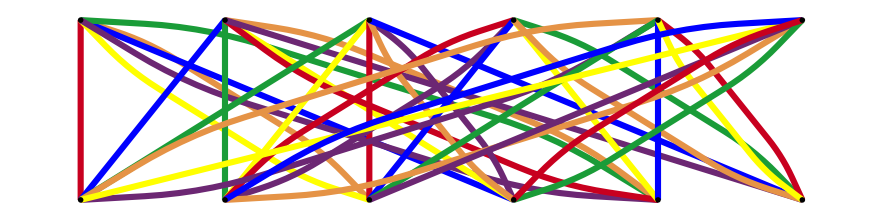

```mathematica
graphadinkra[RandomChoice[PermMat[#],#],buildrules[{{1,2,3,4,5,6},{7,8,9,10,11,12}}],#]&[6]
```

```mathematica
Range[16,32]
```

{16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32}

```mathematica
MatrixForm/@Table[Partition[RandomSample@Flatten@IdentityMatrix[16],16],16]
```

{(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)}

```mathematica
Table[Partition[RandomSample@Flatten@IdentityMatrix[16],16],16];
```

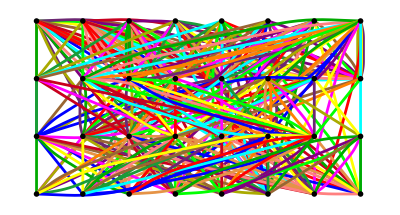

```mathematica
graphadinkra[

Table[Partition[RandomSample@Flatten@IdentityMatrix[16],16],16]

,buildrules[{{1,2,3,4,5,6,7,8},{17,18,19,20,21,22,23,24},{9,10,11,12,13,14,15,16},{25,26,27,28,29,30,31,32}}],16]
```

```mathematica
Flatten@Table[{1,0,0,0,0,0,0,0,0,0,0,0,0},{i,12}]
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Count[Flatten@Table[{1,0,0,0,0,0,0,0,0,0,0,0},{i,12}],1]
```

12

### Yangrui

```mathematica
singlecolor={{1,1,1,0,0,0,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0}};
```

```mathematica
blabel={1,165,330,1144,4290,5005,7865,17160,1,165,330,1};
flabel={32,1408,3520,32};
```

```mathematica
graphyangrui[matlist_,raise_,num_]:=
GraphPlot[
listToEdge[matlist,num],
EdgeRenderingFunction->(Switch[Sign@#3,
1,{Clist[[Abs@#3]],Thickness[0.005],Line[#1]},
-1,{Clist[[Abs@#3]],Dashing[{0.025,0.047}],Thickness[0.005],Line[#1]}
]&)
,VertexRenderingFunction->(If[#2≤num,
Inset[Graphics[{Black,EdgeForm[Thickness[0.1]],Disk[{0,0},.04],White,Text[Style[flabel[[#2]],13],{0,0}]},ImageSize->60],#],
Inset[Graphics[{White,EdgeForm[Thickness[0.1]],Disk[{0,0},.04],Black,Text[Style[blabel[[#2-num]],13],{0,0}]},ImageSize->60],#]
]&)
,VertexCoordinateRules->raise
]
```

```mathematica
MatrixForm/@Table[Partition[RandomSample@Flatten@Flatten@Table[{1,0,0,0,0,0,0,0,0,0,0,0},{i,12}],12],12];
```

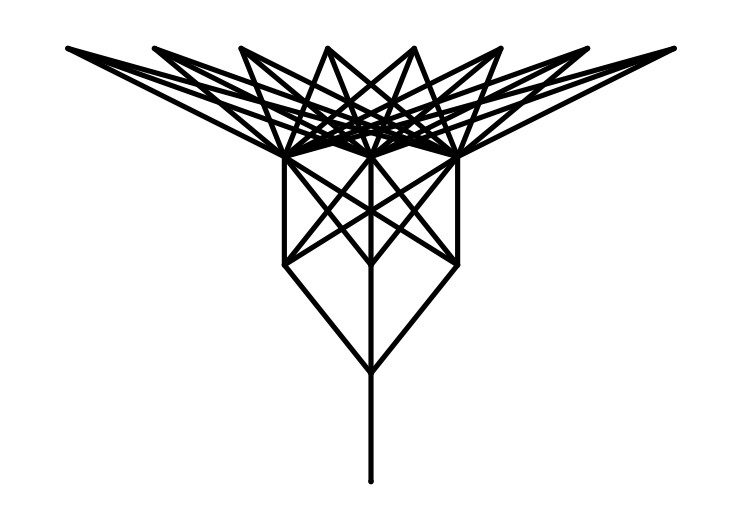

```mathematica
graphyangrui[{singlecolor},buildrules[{{5,6,7,8,9,10,11,12},{1,2,3},{13,14,15},{4},{16}}],4]
```

```mathematica
Export["/home/icarus/Downloads/Yangrui.png",%13,"PNG"]
```

/home/icarus/Downloads/Yangrui.png

### Polishes

Change function names fit Mathematica standard (FirstLettersAreCapitalized)
Add RGB color
Add Manipulate buttons for shape of circles and font/bold/etc empty rectangles circles ovals
Arbitrary image files for node labels
Add dot-dot-dot or empty edges or something to denote “subset” of a full adinkra